==============================================================================
This file is part of the 3D3A Mathematica Toolbox.
   
Contributing author(s), listed alphabetically by last name:
Joseph G. Tylka <josephgt@princeton.edu>
3D Audio and Applied Acoustics (3D3A) Laboratory
Princeton University, Princeton, New Jersey 08544, USA
   
MIT License
   
Copyright (c) 2018 Princeton University
   
Permission is hereby granted, free of charge, to any person obtaining a copy
of this software and associated documentation files (the “Software”), to deal
in the Software without restriction, including without limitation the rights
to use, copy, modify, merge, publish, distribute, sublicense, and/or sell
copies of the Software, and to permit persons to whom the Software is
furnished to do so, subject to the following conditions:
   
The above copyright notice and this permission notice shall be included in all
copies or substantial portions of the Software.
   
THE SOFTWARE IS PROVIDED “AS IS”, WITHOUT WARRANTY OF ANY KIND, EXPRESS OR
IMPLIED, INCLUDING BUT NOT LIMITED TO THE WARRANTIES OF MERCHANTABILITY,
FITNESS FOR A PARTICULAR PURPOSE AND NONINFRINGEMENT. IN NO EVENT SHALL THE
AUTHORS OR COPYRIGHT HOLDERS BE LIABLE FOR ANY CLAIM, DAMAGES OR OTHER
LIABILITY, WHETHER IN AN ACTION OF CONTRACT, TORT OR OTHERWISE, ARISING FROM,
OUT OF OR IN CONNECTION WITH THE SOFTWARE OR THE USE OR OTHER DEALINGS IN THE
SOFTWARE.
==============================================================================

```mathematica
Needs["general`"]
Needs["dsp`"]
```

```mathematica
filePath = SystemDialogInput["FileOpen"];
IRList = sweepToIR2[filePath][[1]];
```

#### Plotting

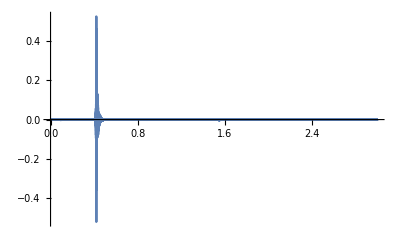

```mathematica
Fs = getSamplingRate[filePath];
IRLen = Length[IRList[[1,1]]];
t = timeList[IRLen,Fs];
ListPlot[Transpose[{t,IRList[[2,2]]}],Joined->True,PlotRange->All]
```

#### Diagnostics

```mathematica
signalOnset[IRList[[2,2]],"Threshold"->10]
Max[Abs[IRList[[2,2]]]]
Sqrt[Mean[Abs[IRList[[2,2]]]^2]]
Mean[Abs[IRList[[2,2]]]]
```

20009

0.524472

0.00612832

0.000983939